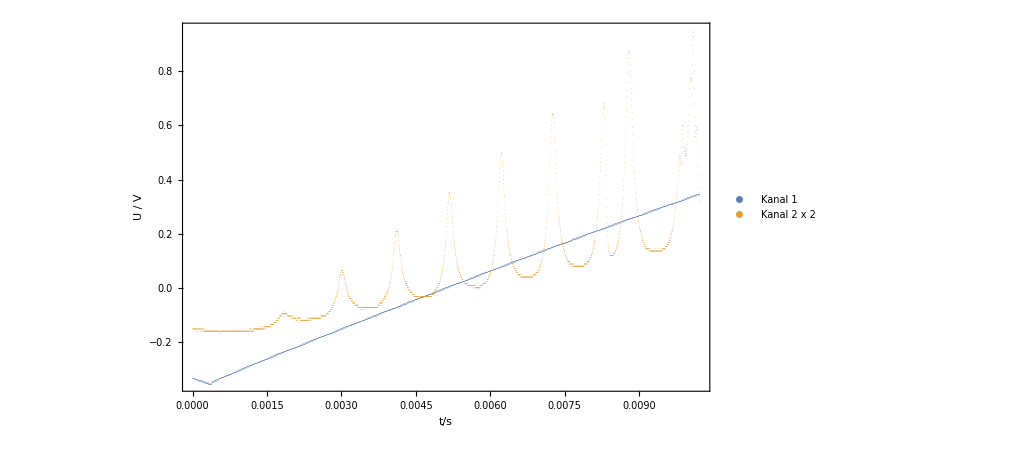

```mathematica
path = "./04.16/up-etalon_zoom.tab";
ch1zoom = 1;
ch2zoom = 2;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

```mathematica
Ramp={{0.009976,0.3267},{0.0006967,-0.326}};
SlopeRamp=(Ramp[[1,2]]-Ramp[[2,2]])/(Ramp[[1,1]]-Ramp[[2,1]])(*V/s*)
SlopeRamp2=SlopeRamp*40*10^-3(*mA/ms*)
```

70.3394

2.81357

{3.016,4.138,5.2,6.231,7.277,8.323}

{8.48574,11.6426,14.6306,17.5314,20.4744,23.4174}

{0.,9.924,19.848,29.772,39.696,49.62}

| Estimate | Standard Error | t-Statistic | P-Value
a | -28.6907 | 0.375873 | -76.3307 | 1.76546×10^-7
b | 3.33746 | 0.022353 | 149.307 | 1.20698×10^-8

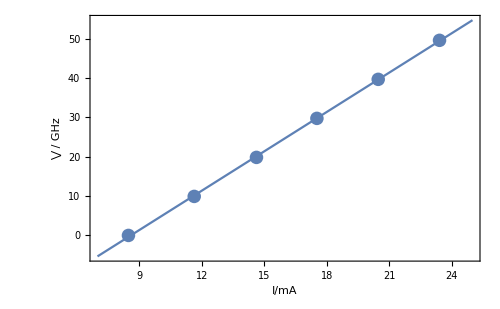

3.33746

```mathematica
Maxpos=Transpose[{{0.003016,0.06229},{0.004138,0.2129},{0.0052,0.3502},{0.006231,0.5008},{0.007277,0.6414},{0.008323,0.6916}}][[1]]1000
Maxpos=%*SlopeRamp2
nus=Table[9.924i,{i,0,Length[Maxpos]-1}]
data=Transpose[{Maxpos,nus}];
nlm=NonlinearModelFit[data,a + b x,{a,b},x];
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,7,25},Frame->True,FrameLabel->{"I/mA","⋁ / GHz"},ImageSize->500],ListPlot[data]]
GHzmA=nlm["ParameterTableEntries"][[2,1]](*GHz/mA*)
```

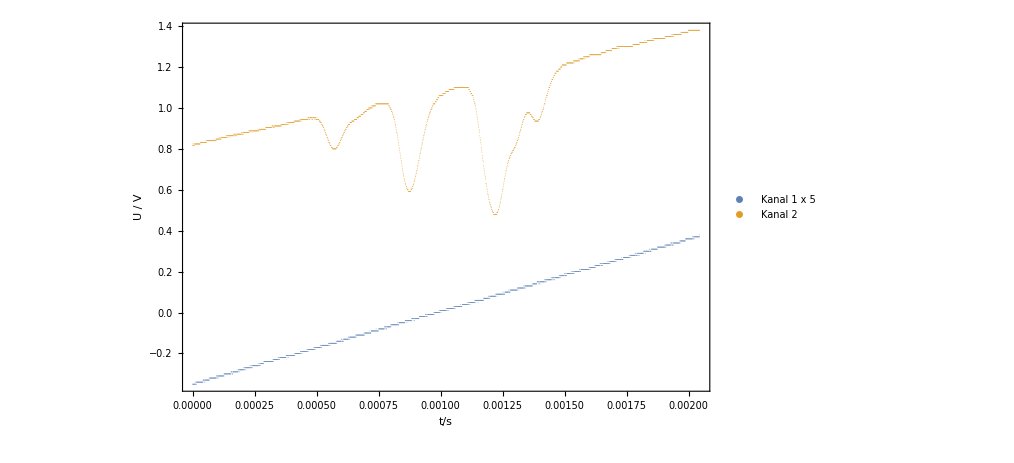

```mathematica
path = "./04.16/up-hfs_zoom.tab";
ch1zoom = 5;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

```mathematica
MinPos=Transpose[{{0.0005699,0.801},{0.000657,0.937},{0.0008761,0.5953},{0.001224,0.4777},{0.001299,0.8084},{0.001393,0.9296}}][[1]]
```

{0.0005699,0.000657,0.0008761,0.001224,0.001299,0.001393}

```mathematica
Ramp2={{0.001987,0.3561},{0.0001195,-0.3102}};
SlopeRamp3=(Ramp2[[1,2]]-Ramp2[[2,2]])/(Ramp2[[1,1]]-Ramp2[[2,1]])/5(*V/s*)
SlopeRamp4=SlopeRamp3*40*10^-3(*mA/ms*)
```

71.3574

2.8543

```mathematica
Measvals=MinPos*SlopeRamp4*GHzmA 1000
```

{5.42893,6.25865,8.34582,11.66,12.3744,13.2699}

```mathematica
spectrum={-3.07,-2.25,Mean[{-1.48,-1.12}],Mean[{1.56,1.92}],3.76,4.58}
```

{-3.07,-2.25,-1.3,1.74,3.76,4.58}

FittedModel[-8.53157+0.953116 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | -8.53157 | 0.921693 | -9.25642 | 0.000757394
b | 1.04919 | 0.101168 | 10.3708 | 0.000488042

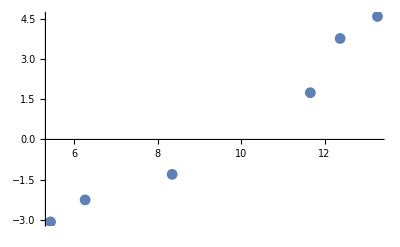

```mathematica
data=Transpose[{Measvals,spectrum}];
nlm=NonlinearModelFit[data,a+x/b,{a,b},x]
nlm["ParameterTable"]
ListPlot[data]
```